```mathematica
(* 
 Ahmed Qureshi
404335525
ahmed.qureshi@ucla.edu
hw 4
*)
```

```mathematica
(*1*)
Remove["Global`*"]
$Assumptions = {Element[{β,γ,c},Reals]};

βeq = Solve[γ==1/Sqrt[1-β^2],β][[2]];
γeq = γ->1/Sqrt[1-β^2];
L4v[β_]={{γ,γ*β,0,0},{γ*β,γ,0,0},{0,0,1,0},{0,0,0,1}};
r  = {t, x, y,z};
L4vinverse[β_]=Inverse[L4v[β]]//Simplify;
L4vinv[β_] = {{γ,-γ*β,0,0},{-γ*β,γ,0,0},{0,0,1,0},{0,0,0,1}};

rp = L4vinverse[β].r;
rp//MatrixForm//Simplify;

Print["Inverse operator mapping lab frame to rocket frame = ", L4vinverse[β]//MatrixForm//Simplify]
Print["Simplifies to = ",L4vinv[β]//MatrixForm]
Print["Similar to the operator mappingfrom rocket to lab frame ",L4v[β]//MatrixForm]
Print["Differnce is i β signs which are opposite and represent the difference i relative velocities of the frames."]
```

Inverse operator mapping lab frame to rocket frame = (1/(γ-β^2 γ) | β/((-1+β^2) γ) | 0 | 0
β/((-1+β^2) γ) | 1/(γ-β^2 γ) | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Simplifies to = (γ | -β γ | 0 | 0
-β γ | γ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Similar to the operator mappingfrom rocket to lab frame (γ | β γ | 0 | 0
β γ | γ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Differnce is i β signs which are opposite and represent the difference i relative velocities of the frames.

```mathematica
(*2*)
Remove["Global`*"]
SetAttributes[{c,β,c,γ,θ,ϕ},Constant]
$Assumptions = {Element[{c,β,c,γ,θ,ϕ},Reals]};

L4v[β_]={{γ,γ*β,0,0},{γ*β,γ,0,0},{0,0,1,0},{0,0,0,1}};
βeq = Solve[γ==1/Sqrt[1-β^2],β][[2]];

rp = {c*tp,c*tp*Sin[θ]*Cos[ϕ],c*tp*Sin[θ]*Sin[ϕ],c*tp*Cos[θ]};
Print["2)(i) Rocket frame four vector = ",rp//MatrixForm]

r = L4v[β].rp;
Print["(ii) Lab frame vector= ",r//MatrixForm]

dsq = r[[2]]^2+r[[3]]^2+r[[4]]^2//Simplify;
tsq = (r[[1]]/c)^2;
vsq=(dsq/tsq)/.βeq//FullSimplify;
v= Sqrt[vsq];

Print["(iii) The speed of the photon = ",c]
```

2)(i) Rocket frame four vector = (c tp
c tp Cos[ϕ] Sin[θ]
c tp Sin[θ] Sin[ϕ]
c tp Cos[θ])

(ii) Lab frame vector= (c tp γ+c tp β γ Cos[ϕ] Sin[θ]
c tp β γ+c tp γ Cos[ϕ] Sin[θ]
c tp Sin[θ] Sin[ϕ]
c tp Cos[θ])

(iii) The speed of the photon = c

```mathematica
(*3*)
Remove["Global`*"]

γ=1/Sqrt[1-v^2/c^2];
x[i_]:=γ*(xp[i]+v*tp[i]);
y[i_]:=yp[i];
z[i_]:=zp[i];
t[i_]:=γ*(tp[i]+v*xp[i]/c^2);

Δt= t[2]-t[1];
Δtd= Δt/.xp[1]->xp[2]//Simplify;
Print["3)(i) Time Dilation = ", Δtd]

Δts=Δt/.tp[1]->tp[2]//Simplify;
Print["(ii)Simultaneous events i the rocket frame are not simultaneous i the lab as Δt ≠ 0, = ", Δts]

sim=tp[1]->tp[2];
L=(x[2]-x[1]//Simplify)/.sim;
Print["(iii) Length contraction = ",L]

Remove["Global`*"];
γ=1/Sqrt[1-v^2/c^2];
x[i_,v_]:=γ*(xp[i]+v*tp[i]);
y[i_,v_]:=yp[i];
z[i_,v_]:=zp[i];
t[i_,v_]:=γ*(tp[i]+v*xp[i]/c^2);

Lp=(xp[2]-xp[1])->lp;
βeq = (v/c)^2->β^2;
sim=tp[1]->tp[2];
L[v_] = x[2,v]-x[1,v];
L[β_]=L[v]/.Lp/.βeq/.sim;

lp=5;
θ'=π/6;
tp[1]=0;
xp[1]=lp*Cos[θ'];
yp[1]=lp*Sin[θ'];
x[1,β_]=(x[1,v]/γ^2)/.βeq;
y[1,β_]=y[1,v]/.βeq;

Print["(iv) Stick as it would appear i lab"]
Manipulate[ListLinePlot[{{0,0},{x[1,β],y[1,β]}},PlotRange->{{0,5},{0,5}},AxesLabel->{x,y},PlotLabel->"Lab Frame"],{β,0,0.9999}]
```

3)(i) Time Dilation = (-tp[1]+tp[2])/(√(1-v^2/c^2))

(ii)Simultaneous events i the rocket frame are not simultaneous i the lab as Δt ≠ 0, = (v (-xp[1]+xp[2]))/(c^2 √(1-v^2/c^2))

(iii) Length contraction = (-xp[1]+xp[2])/(√(1-v^2/c^2))

(iv) Stick as it would appear i lab

```mathematica
(*4*)
Remove["Global`*"]
SetAttributes[{β,c,Vx,up},Constant];
$Assumptions = {Element[{c,β,γ,Vx},Reals] && c>0};
β=(Vx)/c;
βeq = Solve[γ==1/Sqrt[1-β^2],β][[2]];//Quiet
γeq = γ->(1/Sqrt[1-β^2]);
tp=(L/up);
L4v[β_]={{γ,γ*β,0,0},{γ*β,γ,0,0},{0,0,1,0},{0,0,0,1}};

rp = {c*tp,up*tp*Cos[θ],up*tp*Sin[θ],0};
r=L4v[β].rp//Simplify;
r=r/.γeq;

Print["4) The travel time i outpost frame = ", r[[1]]]

d=Sqrt[(r[[2]])^2+(r[[3]])^2];
d=d/.γeq;
Print["(ii)The traveled distance i outpost frame = ", d]

v=d/(r[[1]])//Simplify;
v=v/.γeq;
Print["(iii)The rover velocity i outpost frame = ",v]

Print["
(iv)The length of the plane can be measured using length contraction yet can't also be used to find the distance traveled by the rover as the bottom and top of the ramp are not not simultaneous i the rocket's frame"]
```

4) The travel time i outpost frame = (c L)/(up √(1-Vx^2/c^2))+(L Vx Cos[θ])/(c √(1-Vx^2/c^2))

(ii)The traveled distance i outpost frame = √((L^2 (Vx+up Cos[θ])^2)/(up^2 (1-Vx^2/c^2))+L^2 Sin[θ]^2)

(iii)The rover velocity i outpost frame = (c up √(1-Vx^2/c^2) √(L^2 ((Vx+up Cos[θ])^2/(up^2 (1-Vx^2/c^2))+Sin[θ]^2)))/(L (c^2+up Vx Cos[θ]))

(iv)The length of the plane can be measured using length contraction yet can't also be used to find the distance traveled by the rover as the bottom and top of the ramp are not not simultaneous i the rocket's frame

```mathematica
(*5*)
Remove["Global`*"]
$Assumptions = {Element[{β,γ,c},Reals]};

L4v[β_]={{γ,γ*β,0,0},{γ*β,γ,0,0},{0,0,1,0},{0,0,0,1}};
βeq = Solve[γ==1/Sqrt[1-β^2],β][[2]];
rp = {c*tp,upx*tp,upy*tp,upz*tp};

Print["5)(i) Space time coordinates i rocket frame = ", rp//MatrixForm]

r = L4v[β].rp//Simplify;
Print["(ii) i the lab frame = ", r//MatrixForm]

ux = r[[2]]/r[[1]]//Simplify;
uy=r[[3]]/r[[1]]//Simplify;
uz=r[[4]]/r[[1]]//Simplify;
Print["(iii) Velocity x, y, z, components i lab frame = ",ux,",", uy,",", uz]
```

5)(i) Space time coordinates i rocket frame = (c tp
tp upx
tp upy
tp upz)

(ii) i the lab frame = (tp (c+upx β) γ
tp (upx+c β) γ
tp upy
tp upz)

(iii) Velocity x, y, z, components i lab frame = (upx+c β)/(c+upx β),upy/(c γ+upx β γ),upz/(c γ+upx β γ)

```mathematica
(*6*)
Remove["Global`*"]
SetAttributes[{β,c},Constant];
$Assumptions = {Element[{c,β,γ},Reals] && c>0};

L4v[β_]={{γ,γ*β,0,0},{γ*β,γ,0,0},{0,0,1,0},{0,0,0,1}};
βeq = Solve[γ==1/Sqrt[1-β^2],β][[2]];
γeq = γ->(1/Sqrt[1-β^2]);
rp = {c*tp,xp,yp,zp};
r = L4v[β].rp;

rpip = (rp[[1]])^2-(rp[[2]])^2-+(rp[[3]])^2-(rp[[4]])^2;
rip=(r[[1]])^2-(r[[2]])^2-+(r[[3]])^2-(r[[4]])^2//FullSimplify;
rip=rip/.γeq//Simplify;

Print["6)(i) Inner product rocket frame ='",rpip]
Print["Inner product lab frame = ",rip]
Print["They are the same"]

p={c,vx,vy,vz}*γp*m;
p2={E/c,Px,Py,Pz};

pip = (p[[1]])^2-(p[[2]])^2-(p[[3]])^2-(p[[4]])^2//Simplify;
p2ip = (p2[[1]])^2-(p2[[2]])^2-(p2[[3]])^2-(p2[[4]])^2;
γp = 1/Sqrt[1-β^2];
Print["(ii) Inner product P.P = ",p2ip]

pp = {m*c,0,0,0};
ppip=pp.pp ;
Print["i moving frame P'.P' = ",ppip]
Print["This must equal P.P =>", ppip ," = ", p2ip]

m=0;
Erule=Solve[p2ip==ppip/.(E^2)->ESq,ESq];
ESq=ESq/.Erule[[1]];
Print["Massless particle E^2 = ",ESq]
Print["Massless particles still have momentum"]

Clear[m]
pt=Series[p[[1]],{β,0,2}];
Print["(iii) Taylor expanding Pt = ",pt]
Print["First term = rest energy, second term = classical kinetic"]
```

6)(i) Inner product rocket frame ='c^2 tp^2-xp^2-yp^2-zp^2

Inner product lab frame = c^2 tp^2-xp^2-yp^2-zp^2

They are the same

(ii) Inner product P.P = ⅇ^2/c^2-Px^2-Py^2-Pz^2

i moving frame P'.P' = c^2 m^2

This must equal P.P =>c^2 m^2 = ⅇ^2/c^2-Px^2-Py^2-Pz^2

Massless particle E^2 = c^2 (Px^2+Py^2+Pz^2)

Massless particles still have momentum

(iii) Taylor expanding Pt = c m+1/2 c m β^2+O[β]^3

First term = rest energy, second term = classical kinetic

7)Light cone in rest frame

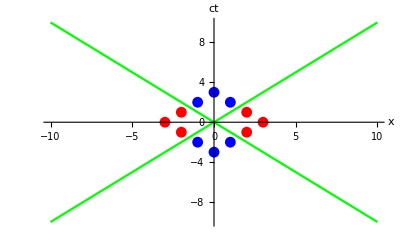

Relative frame

```mathematica
(*7*)
Remove["Global`*"]
Clear[γ,v,β]
β=v/c;
L4v[v_]={{-γ*β,γ},{γ,-γ*β}};
γeq = γ->(1/Sqrt[1-(v/c)^2]);
plot:=Plot[{x,-x},{x,-10,10},{PlotStyle->{Green,Green}},AxesLabel->{x,ct},PlotRange->{{-10,10},{-10,10}}];

i[1]={1,2};
i[2]={-1,2};
i[3]={-1,-2};
i[4]={1,-2};
i[5]={0,3};
i[6] = {0,-3};
j[1]={2,1};
j[2]={2,-1};
j[3]={-2,-1};
j[4]={-2,1};
j[5]={3,0};
j[6] = {-3, 0};

ipts = Table[i[n],{n,1,6}];
jpts = Table[j[n],{n,1,6}];
rest = ListPlot[{ipts,jpts},PlotStyle->{Blue,Red}];

Print["7)Light cone in rest frame"]
Show[plot,rest]

i2[1][v_]=L4v[v].i[1];
i2[2][v_]=L4v[v].i[2];
i2[3][v_]=L4v[v].i[3];
i2[4][v_]=L4v[v].i[4];
i2[5][v_]=L4v[v].i[5];
i2[6][v_]=L4v[v].i[6];
j2[1][v_]=L4v[v].j[1];
j2[2][v_]=L4v[v].j[2];
j2[3][v_]=L4v[v].j[3];
j2[4][v_]=L4v[v].j[4];
j2[5][v_]=L4v[v].j[5];
j2[6][v_]=L4v[v].j[6];

i2pts[v_] = Table[i2[n][v],{n,1,6}]/.γeq;
j2pts[v_]= Table[j2[n][v],{n,1,6}]/.γeq;
pts[v_] := ListPlot[{i2pts[v],j2pts[v]},PlotStyle->{Blue,Red}];

c=1;
x[v_]=1/(v/c)*x;
xp[v_]=v/c*x;

plotp[v_]:=Plot[{-x,x},{x,-10,10},{PlotStyle->{Green,Green}},AxesLabel->{"x'","ct'"},PlotRange->{{-10,10},{-10,10}}];
show[v_]:=Show[plotp[v],pts[v]]
Print["Relative frame"]
Manipulate[show[v],{v,0,0.9999}]
```